## Introduction

Created by K . D .Dzikowski		2022

## Description

A summary of some of the intresting mathematical results that I encounetered during my phd

## Code

### Generating integral of the step function ∫E^(-xr-yr')θ(r-r')r^a(r')^bⅆrⅆr'

```mathematica
NoNRegularizer[a_,b_,x_,y_]:=Module[{},Gamma[a+b]/(a x^(b+a))Hypergeometric2F1[a,a+b,a+1,-y/x]]
```

### Imaginary part of the complex power function

```mathematica
Im[(ⅈ k+β)^(1+q)]==(q+1)k  β^q Hypergeometric2F1[1/2-q/2,-q/2,3/2,-k^2/β^2]
```

### Simple closed form of the infinite sum of hypergeometric functions

```mathematica
Sum[(y^n a Gamma[b+n] Hypergeometric2F1[a+n,b+n,a+n+1,x])/((a+n) Gamma[b] n!),{n,0,∞}]==Hypergeometric2F1[a,b,a+1,x+y]
```

### Derivative of the first confluent hypergeometric function over the first parameter at 0

```mathematica
Derivative[1,0,0][Hypergeometric1F1][0,b,x]=x/b HypergeometricPFQ[{1,1},{2,1+b},x]
```

### Simplification of the 3F2 hypergeometric function for x=1 and integer parameters (b and c can also be non-integer)

```mathematica
HypergeometricPFQ[{1,2,b},{c,m},1]==- (((c-2)(c-1)(1-m) (2-m))/(Gamma[b]Gamma[c-b])Gamma[1+b-m] Gamma[-3-b+c+m] (-HarmonicNumber[-3+c]+HarmonicNumber[-4-b+c+m])+Gamma[c]/Gamma[b] Sum[((m-1)!(-1)^k)/(k!(m-k-3)!)Sum[Gamma[-1+b+j-k]/(Gamma[-1+c+j-k](j+1)),{j,0,k}],{k,0,-3+m}])
```

### Explicit form of the second confluent hypergeometric function for a negative integer value of the second parameter

```mathematica
HypergeometricU[a,-n,z]==Polynom[n,a-1,-z]/((a+n)!)-Log[z](-z)^(n+1)/Gamma[a] Hypergeometric1F1Regularized[a+n+1,n+2,z]+∑_100^(k=n+1) ((-1)^n Binomial[a-1+k,a+n])/Gamma[a](PolyGamma[a+k]-PolyGamma[k-n]-PolyGamma[k+1]) z^k/(k!)
```

```mathematica
Polynom[n_,l_,x_]:=Module[{},∑_n^(k=0) x^k Binomial[l+k,k](n-k)!]
```

### Magic

```mathematica
HypergeometricPFQRegularized[{1,1},{2,2-i},x]/x^(i-1)==Hypergeometric1F1[i,i+1,x]/i
```

### A particularly interesting function that attains all values (-1,1) but in a very chaotic order e.g. one cannot easily find the region where | f | > 0.999

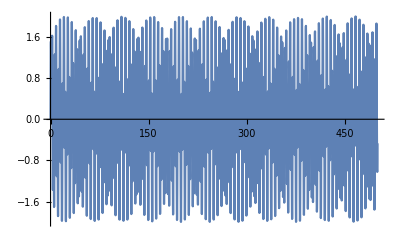

```mathematica
Plot[Sin[x]+Sin[π x],{x,0,500}]
```